# Analiza globalnega segrevanja

## Projektna naloga pri predmetu ROM

Namen projekta je analizirati dolgoročne spremembe temperature na več izbranih lokacijah po svetu s pomočjo podatkov WeatherData v Wolfram Language. 
Analiza vključuje mesečne in letne povprečne temperature, temperaturne anomalije, linearni trend segrevanja ter primer padavin. 
Projekt je zasnovan tako, da se vsa koda izvede na poljubnem računalniku z Mathematica/Wolfram Language in internetno povezavo. Uporabljene so relativne poti glede na lokacijo beležnice.

## 1. Priprava okolja

Najprej počistimo prejšnje definicije in nastavimo relativno mapo data znotraj mape projekta. Tako projekt ne uporablja absolutnih lokalnih poti.

```mathematica
ClearAll["Global`*"];

projectDir = NotebookDirectory[];
dataDir = FileNameJoin[{projectDir, "data"}];
If[!DirectoryQ[dataDir], CreateDirectory[dataDir]];

Print["Projektna mapa: ", projectDir];
Print["Mapa za podatke: ", dataDir];
```

Projektna mapa: D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\

Mapa za podatke: D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data

## 2. Izbrane lokacije in časovno obdobje

Izbranih je pet mest z različnih delov sveta. Lokacije podamo s koordinatami, kar je za WeatherData prenosljivo in neodvisno od lokalnih nastavitev. Analiziramo obdobje 1990–2024.

```mathematica
locations = <|
   "Ljubljana" -> {46.0569, 14.5058},
   "London" -> {51.5074, -0.1278},
   "New York" -> {40.7128, -74.0060},
   "Tokyo" -> {35.6762, 139.6503},
   "Sydney" -> {-33.8688, 151.2093}
|>;

startDate = {1990, 1, 1};
endDate = {2024, 12, 31};

Dataset[
  KeyValueMap[
    <|"Mesto" -> #1, "Koordinate" -> #2|> &,
    locations
  ]
]
```

## 3. Lastne funkcije za pridobivanje in čiščenje podatkov

Za naprednejši del projekta definiramo več lastnih funkcij z Module. Funkcija getTemperatureData pridobi mesečne povprečne temperature, cleanSeries pretvori količine v želene enote in odstrani neveljavne vrednosti, annualMean pa iz mesečnih podatkov izračuna letna povprečja.

```mathematica
ClearAll[cleanSeries, getTemperatureData, getPrecipitationData, yearOf, annualMean, annualSum];

cleanSeries[data_, unit_] := Module[{pairs},
  pairs = Normal[data];
  Map[
    {#[[1]], N[QuantityMagnitude[UnitConvert[#[[2]], unit]]]} &,
    pairs
  ]
];
getTemperatureData[coords_] := Module[{raw},
  raw = WeatherData[
    coords,
    "MeanTemperature",
    {startDate, endDate, "Month"}
  ];
  cleanSeries[raw, "DegreesCelsius"]
];

getPrecipitationData[coords_, from_, to_] := Module[{raw, pairs},
  raw = WeatherData[
    coords,
    "TotalPrecipitation",
    {from, to, "Month"}
  ];

  pairs = Normal[raw];

  Map[
    {#[[1]], N[10 #[[2]]]} &,
    pairs
  ]
];

yearOf[d_] := DateValue[DateObject[d], "Year"];

annualMean[data_] := Module[{grouped},
  grouped = GroupBy[
    data,
    yearOf[First[#]] & -> Last
  ];

  SortBy[
    KeyValueMap[
      {#1, Mean[#2]} &,
      grouped
    ],
    First
  ]
];

annualSum[data_] := Module[{grouped},
  grouped = GroupBy[
    data,
    yearOf[First[#]] & -> Last
  ];

  SortBy[
    KeyValueMap[
      {#1, Total[#2]} &,
      grouped
    ],
    First
  ]
];
```

## 4. Pridobivanje temperaturnih podatkov z Map

Funkcijo getTemperatureData uporabimo nad vsemi lokacijami z Map. Rezultat je Association, kjer je za vsako mesto shranjena časovna vrsta mesečnih temperatur.

```mathematica
temperatureMonthly = AssociationThread[
  Keys[locations],
  Map[getTemperatureData, Values[locations]]
];

(* Shranimo kopijo obdelanih podatkov v prenosljivi relativni poti. *)
Export[
  FileNameJoin[{dataDir, "temperature_monthly.wl"}],
  temperatureMonthly
];

Map[Length, temperatureMonthly]
```

<|Ljubljana→420,London→420,New York→420,Tokyo→420,Sydney→420|>

## 5. Osnovni prikaz podatkov

Najprej prikažemo mesečne temperature za Ljubljano. Ker so mesečna nihanja velika, je naslednji korak izračun letnih povprečij.

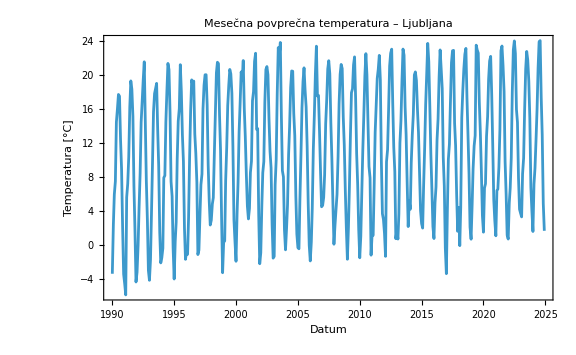

```mathematica
DateListPlot[
  temperatureMonthly["Ljubljana"],
  PlotRange -> All,
  Frame -> True,
  FrameLabel -> {"Datum", "Temperatura [°C]"},
  PlotLabel -> "Mesečna povprečna temperatura – Ljubljana",
  ImageSize -> Large
]
```

## 6. Letna povprečja in primerjava mest

Mesečne podatke pretvorimo v letna povprečja. S tem zmanjšamo sezonsko nihanje in lažje opazimo dolgoročni trend.

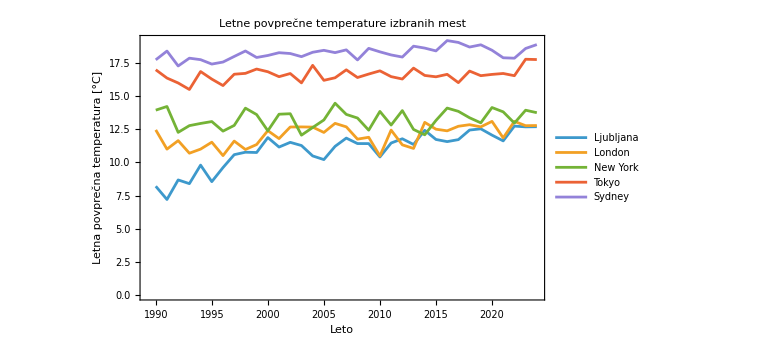

```mathematica
annualByCity = Map[annualMean, temperatureMonthly];

ListLinePlot[
  Values[annualByCity],
  PlotLegends -> Placed[Keys[annualByCity], Right],
  Frame -> True,
  FrameLabel -> {"Leto", "Letna povprečna temperatura [°C]"},
  PlotLabel -> "Letne povprečne temperature izbranih mest",
  PlotRange -> All,
  ImageSize -> Large
]
```

## 7. Temperaturne anomalije glede na obdobje 1991–2020

Temperaturna anomalija pove, za koliko je bilo posamezno leto toplejše ali hladnejše od referenčnega povprečja. Kot osnovno obdobje uporabimo 1991–2020. Pozitivna anomalija pomeni leto nad referenčnim povprečjem.

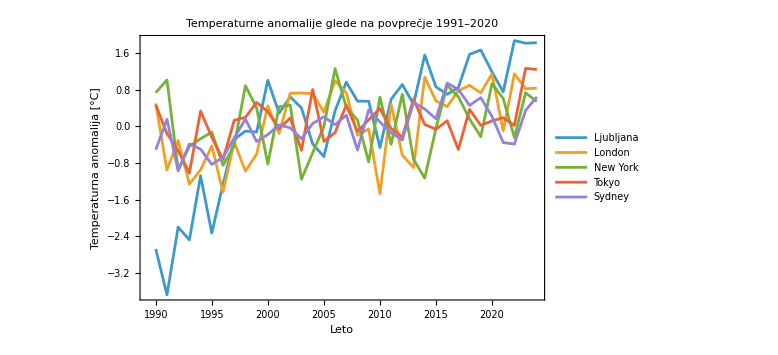

```mathematica
ClearAll[temperatureAnomalies];

temperatureAnomalies[data_] := Module[{baselineValues, baselineMean},
  baselineValues = Cases[
    data,
    {y_, t_} /; 1991 <= y <= 2020 :> t
  ];
  baselineMean = Mean[baselineValues];
  ({#[[1]], #[[2]] - baselineMean} &) /@ data
];

anomaliesByCity = Map[temperatureAnomalies, annualByCity];

ListLinePlot[
  Values[anomaliesByCity],
  PlotLegends -> Placed[Keys[anomaliesByCity], Right],
  Frame -> True,
  FrameLabel -> {"Leto", "Temperaturna anomalija [°C]"},
  PlotLabel -> "Temperaturne anomalije glede na povprečje 1991–2020",
  PlotRange -> All,
  ImageSize -> Large
]
```

## 8. Linearni trend segrevanja

Za vsako mesto prilagodimo linearni model T = a + b·leto. Naklon b pretvorimo v °C na desetletje. To ni napoved prihodnosti, temveč opis linearnega trenda v analiziranem obdobju.

```mathematica
ClearAll[trendSummary];

trendSummary[name_, data_] := Module[
  {model, params, slopeYear, slopeDecade, r2, minYear, maxYear, tempRange},

  model = LinearModelFit[data, {1, x}, x];
  params = model["BestFitParameters"];
  slopeYear = params[[2]];
  slopeDecade = 10 slopeYear;
  r2 = model["RSquared"];
  minYear = Min[data[[All, 1]]];
  maxYear = Max[data[[All, 1]]];

  (* Primer uporabe Apply: razpon opaženih letnih temperatur. *)
  tempRange = Apply[Subtract, Reverse[MinMax[data[[All, 2]]]]];

  <|
    "City" -> name,
    "From" -> minYear,
    "To" -> maxYear,
    "SlopeCPerDecade" -> N[slopeDecade, 4],
    "RSquared" -> N[r2, 4],
    "ObservedTemperatureRangeC" -> N[tempRange, 4]
  |>
];

trendResults = MapThread[
  trendSummary,
  {Keys[annualByCity], Values[annualByCity]}
];

summaryDataset = Dataset[trendResults];
summaryDataset
```

## 9. Poizvedbe z Query

Dataset omogoča pregledno delo s tabelaričnimi rezultati. Z Query izberemo najpomembnejše stolpce in poiščemo mesto z največjim ocenjenim linearnim trendom.

```mathematica
Query[All, {"City", "SlopeCPerDecade", "RSquared"}][summaryDataset]
```

```mathematica
Query[
  MaximalBy["SlopeCPerDecade"],
  {"City", "SlopeCPerDecade"}
][summaryDataset]
```

## 10. Podroben trend za Ljubljano

Spodnji graf združi dejanska letna povprečja in linearni model za Ljubljano.

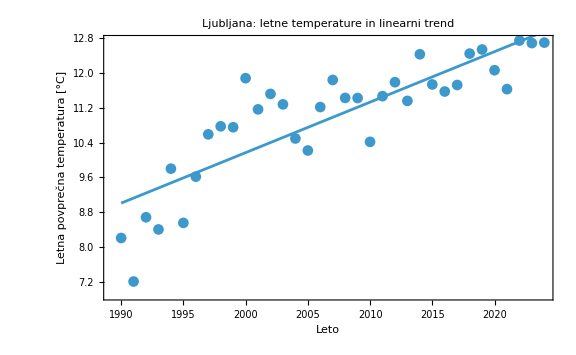

```mathematica
ljData = annualByCity["Ljubljana"];
ljModel = LinearModelFit[ljData, {1, x}, x];

Show[
  ListPlot[
    ljData,
    Frame -> True,
    FrameLabel -> {"Leto", "Letna povprečna temperatura [°C]"},
    PlotLabel -> "Ljubljana: letne temperature in linearni trend",
    PlotMarkers -> Automatic
  ],
  Plot[
    ljModel[x],
    {x, Min[ljData[[All, 1]]], Max[ljData[[All, 1]]]}
  ],
  ImageSize -> Large
]
```

## 11. Dodatna analiza padavin

Poleg temperature analiziramo tudi letne vsote padavin za Ljubljano v obdobju 2000–2024. S tem pokažemo uporabo druge lastnosti WeatherData in dodamo še en neodvisen vremenski kazalnik.

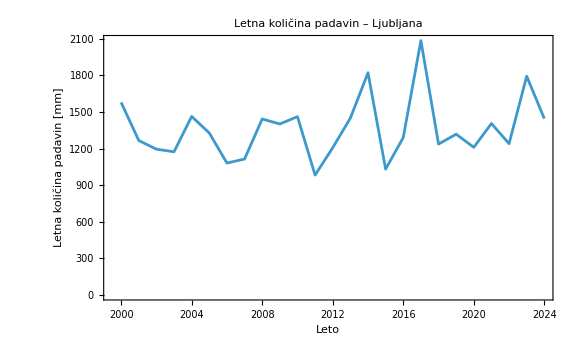

```mathematica
precipitationMonthlyLjubljana = getPrecipitationData[
  locations["Ljubljana"],
  {2000, 1, 1},
  {2024, 12, 31}
];

precipitationAnnualLjubljana = annualSum[precipitationMonthlyLjubljana];

ListLinePlot[
  precipitationAnnualLjubljana,
  Frame -> True,
  FrameLabel -> {"Leto", "Letna količina padavin [mm]"},
  PlotLabel -> "Letna količina padavin – Ljubljana",
  PlotRange -> All,
  ImageSize -> Large
]
```

## 12. Izvoz rezultatov

Ključne rezultate izvozimo v mapo data. Ker uporabljamo NotebookDirectory in FileNameJoin, se poti samodejno prilagodijo računalniku, na katerem je projekt odprt.

```mathematica
Export[
  FileNameJoin[{dataDir, "trend_summary.csv"}],
  Normal[summaryDataset]
];

Export[
  FileNameJoin[{dataDir, "annual_temperature_ljubljana.csv"}],
  Prepend[ljData, {"Year", "MeanTemperatureC"}]
];

Export[
  FileNameJoin[{dataDir, "annual_precipitation_ljubljana.csv"}],
  Prepend[precipitationAnnualLjubljana, {"Year", "TotalPrecipitationMM"}]
];

FileNames["*", dataDir]
```

{D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data\annual_precipitation_ljubljana.csv,D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data\annual_temperature_ljubljana.csv,D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data\.gitkeep,D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data\temperature_monthly.wl,D:\Faks\ROM\ROM_globalno_segrevanje_projekt\ROM_globalno_segrevanje\data\trend_summary.csv}

## 13. Interpretacija rezultatov

Po izvedbi beležnice tabela trendResults pokaže ocenjeni naklon temperature v °C na desetletje za vsako mesto. Če je naklon pozitiven, se je v analiziranem obdobju na tej lokaciji povprečna temperatura v povprečju zviševala; negativni naklon bi pomenil zniževanje. R.b2 pove, kolikšen delež variabilnosti letnih temperatur pojasni preprost linearni trend.

Pri interpretaciji moramo biti previdni: analiza petih mest ni enaka izračunu globalne povprečne temperature Zemlje. Projekt zato ne trdi, da lokalni podatki sami dokazujejo globalni trend, ampak pokaže, kako lahko z WeatherData, statističnimi metodami in vizualizacijami preučujemo dolgoročne spremembe na izbranih lokacijah.

## 14. Zaključek

Projekt je pokazal celoten potek podatkovne analize v Wolfram Language: pridobivanje podatkov iz WeatherData, čiščenje in pretvorbo enot, delo z Association in Dataset, uporabo lastnih funkcij z Module, uporabo Map, Apply in Query, izračun letnih povprečij in anomalij ter modeliranje trendov z LinearModelFit. Rezultati so predstavljeni z več grafi in tabelo, izbrane rezultate pa je mogoče izvoziti v CSV datoteke.

Za končno oddajo je priporočljivo izvesti vse celice od začetka do konca, preveriti, da ni sporočil o napakah, nato beležnico shraniti skupaj z mapo data in README.md v GitHub repozitorij.

## 15. Viri in dokumentacija

• Wolfram Language Documentation: WeatherData
• Wolfram Language Documentation: LinearModelFit
• Wolfram Language Documentation: Dataset in Query
• Wolfram Language Documentation: DateListPlot in ListLinePlot
• Podatki v projektu se pridobijo neposredno prek funkcije WeatherData ob izvedbi beležnice.